# Virtual Realizations of Quantum Computers

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Quantum Bits

We will be denoting each qubit by the symbol S and accompanying indices .

```mathematica
Let[Qubit,S]
```

The Pauli operators are specified by the last index. For example, the Pauli operator S_j^x is denoted by S[j,1].

```mathematica
S[j,1]
```

S_j^x

```mathematica
S[j,1]**S[j,2]
S[j,1]**S[k,2]
```

ⅈ S_j^z

S_j^x S_k^y

## Dynamical Scheme

### Single-Qubit Gates

Consider a qubit. Let us apply a (fictitious) magnetic field.

```mathematica
Let[Real,B]
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
```

1/2 (B_1 S^x+B_2 S^y+B_3 S^z)

To be specific, we consider the case with the magnetic field between the x-  and z-axis in the xz-plane. The factor of 1/√2is to set the energy (frequency) scale to unit.

```mathematica
B[1]=B[3]=1/Sqrt[2];B[2]=0;
opH
```

1/2 (S^x/(√2)+S^z/(√2))

```mathematica
opU[t_]=MultiplyExp[-I t opH]
opU[t]//Elaborate
```

ⅇ^(-1/2 ⅈ t (S^x/(√2)+S^z/(√2)))

Cos[t/2]-(ⅈ S^x Sin[t/2])/(√2)-(ⅈ S^z Sin[t/2])/(√2)

```mathematica
vec[t_]=opU[t]**Ket[]//Elaborate
```

-(ⅈ 1_S Sin[t/2])/(√2)+␣ (Cos[t/2]-(ⅈ Sin[t/2])/(√2))

This illustrates the Larmor precession (with the qubit regarded as a “spin”).
Technical Note: You need Chop because numerical errors sometimes give 0.+Ket[…], which cannot be handled properly by BlochVector.

```mathematica
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv},ImageSize->Small]
```

-Graphics3D-

Let us now examine the probabilities for the qubit to be found in the logical basis states.

```mathematica
prob[t_]=Abs[Normal@Matrix@vec[t]]^2
```

{(|Cos[t/2]-(ⅈ Sin[t/2])/(√2)|)^2,1/2 (|Sin[t/2]|)^2}

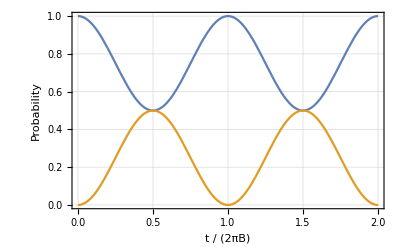

```mathematica
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2πB)","Probability"}]
```

Let us now apply a time-dependent field. It precesses around the z-axis. Note that typically, B_3≫B_1,B_2.

```mathematica
ω=2Pi;
B[1]=Cos[ω t];
B[2]=Sin[ω t];
B[3]=1.1ω; (* near resonance *)
Graphics3D[{Blue,Table[Arrow@Tube@{{0,0,0},B@{1,2,3}},{t,0,1,0.1}]},
PlotRange->ω{{-1,1},{-1,1},{-1,1}},ImageSize->Small]
```

-Graphics3D-

```mathematica
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
```

1/2 (Cos[2 π t] S^x+6.9115 S^z+S^y Sin[2 π t])

```mathematica
opHR=Rotation[-ω t,S[3]]**opH**Rotation[ω t,S[3]]-ω S[3]/2//Elaborate//Chop
```

S^x/2+0.314159 S^z

```mathematica
opUR[t_]=MultiplyExp[-I t opHR]
```

ⅇ^(-ⅈ t (S^x/2+0.314159 S^z))

```mathematica
vec[t_]=opUR[t]**Ket[]//Elaborate;
```

This illustrates the precession in the rotating frame, which is called the Rabi oscillation.

```mathematica
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv},ImageSize->Small]
```

-Graphics3D-

This shows the transition probabilities in the logical basis states. Note that the probabilities are the same both in the lab and rotating frame. The Rabi oscillation frequency is in this particular example is close to one---it is exactly one at resonance.

```mathematica
prob[t_]=Abs[Normal@Matrix@vec[t]]^2;
```

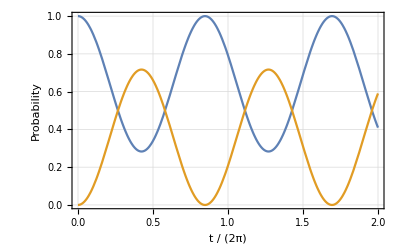

```mathematica
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2π)","Probability"}]
```

Let us consider the case exactly at the resonance.

```mathematica
ω=2Pi;
B[1]=Cos[ω t];
B[2]=Sin[ω t];
B[3]=ω; (* resonance *)
```

```mathematica
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
opHR=Rotation[-ω t,S[3]]**opH**Rotation[ω t,S[3]]-ω S[3]/2//Elaborate//Chop
opUR[t_]=MultiplyExp[-I t opHR]
```

1/2 (Cos[2 π t] S^x+2 π S^z+S^y Sin[2 π t])

S^x/2

ⅇ^(-1/2 ⅈ t S^x)

The Rabi oscillation now corresponds to the Larmor precession around the x-axis in the rotating frame.

```mathematica
vec[t_]=opUR[t]**Ket[]//Elaborate;
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv},ImageSize->Small]
```

-Graphics3D-

As the precession axis is exactly along the x-axis, the maximum transition probability can reach unity.

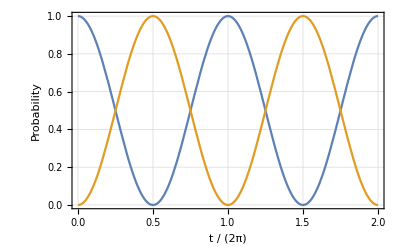

```mathematica
prob[t_]=Abs[Normal@Matrix@vec[t]]^2;
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2π)","Probability"}]
```

### Two-Qubit Gates

Consider the Heisenberg exchange coupling.

```mathematica
op=MultiplyDot[S[1,All],S[2,All]]
```

S_1^x S_2^x+S_1^y S_2^y+S_1^z S_2^z

This is the matrix representation.

```mathematica
mat=Matrix[(1+op)/2];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
opU=MultiplyExp[-I (Pi/4)*(op-1)]
opU//Elaborate
```

ⅇ^(-1/4 ⅈ π (-1+S_1^x S_2^x+S_1^y S_2^y+S_1^z S_2^z))

1/2+1/2 S_1^x S_2^x+1/2 S_1^y S_2^y+1/2 S_1^z S_2^z

```mathematica
matU=Matrix[opU];
matU//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

Next, consider the XY exchange interaction.

```mathematica
op=MultiplyDot[S[1,{1,2}],S[2,{1,2}]]
```

S_1^x S_2^x+S_1^y S_2^y

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 2 | 0
0 | 2 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
opU=MultiplyExp[-I ϕ op]
```

ⅇ^(-ⅈ ϕ (S_1^x S_2^x+S_1^y S_2^y))

```mathematica
Matrix[opU]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[2 ϕ] | -ⅈ Sin[2 ϕ] | 0
0 | -ⅈ Sin[2 ϕ] | Cos[2 ϕ] | 0
0 | 0 | 0 | 1)

Let us now consider the Ising exchange interaction. Here we have introduced an additional single-qubit term controlling the second qubit.

```mathematica
op= S[1,3]+ S[2,3]- S[1,3]**S[2,3]
```

-S_1^z S_2^z+S_1^z+S_2^z

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -3)

```mathematica
opU=MultiplyExp[-I ϕ op]
opU//Matrix//MatrixForm
```

ⅇ^(-ⅈ ϕ (-S_1^z S_2^z+S_1^z+S_2^z))

(ⅇ^(-ⅈ ϕ) | 0 | 0 | 0
0 | ⅇ^(-ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(-ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(3 ⅈ ϕ))

```mathematica
opU=Exp[I Pi/4] MultiplyExp[-I Pi/4 op]
opU//Matrix//MatrixForm
```

ⅇ^((ⅈ π)/4) ⅇ^(-1/4 ⅈ π (-S_1^z S_2^z+S_1^z+S_2^z))

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

## Geometric/Topological Scheme

### A Toy Model

Consider a four-level system.

```mathematica
Let[Qudit,A,Dimension->4]
```

Here is the standard basis of the Hilbert space associated with the system. We will regard 0as the excited level and 1, 2, 3as the ground-state levels.

```mathematica
bs=Basis[A];
bs//LogicalForm
```

{0_A,1_A,2_A,3_A}

The ground states are coupled (each jwith an amplitude Ω_j) to the excited level.

```mathematica
Let[Real,Ω,ϵ]
H=ϵ A[0->0]-(1/2)*PlusDagger@Sum[Ω[j]*A[0->j],{j,1,3}]
```

ϵ (00)+1/2 (-(10) Ω_1-(01) Ω_1-(20) Ω_2-(02) Ω_2-(30) Ω_3-(03) Ω_3)

We choose a parameterization. This parameterization is convenient to normalize various states.

```mathematica
Let[Real,θ,ϕ]
Ω[1]=Sin[θ]Cos[ϕ];
Ω[2]=Sin[θ]Sin[ϕ];
Ω[3]=Cos[θ];
```

Here is the “bright” state in the parameterization.

```mathematica
ketΩ=Sum[Ket[A->j]*Ω[j],{j,1,3}]
```

Cos[θ] 3_A+Cos[ϕ] 1_A Sin[θ]+2_A Sin[θ] Sin[ϕ]

Here is a choice of two “dark” states.

```mathematica
ketD1=Ket[A->1]*Sin[ϕ]-Ket[A->2]*Cos[ϕ]
ketD2=Ket[A->1]*Cos[θ]*Cos[ϕ]+Ket[A->2]*Cos[θ]*Sin[ϕ]-Ket[A->3]*Sin[θ]
```

-Cos[ϕ] 2_A+1_A Sin[ϕ]

Cos[θ] Cos[ϕ] 1_A-3_A Sin[θ]+Cos[θ] 2_A Sin[ϕ]

Let us check if they are indeed “dark” with respect to the Hamiltonian.

```mathematica
H**ketD1
H**ketD2
```

0

0

The two dark state must be orthogonal to the bright state. Let us check it.

```mathematica
new={ketD1,ketD2,ketΩ};
Outer[Multiply,Dagger[new],new]//Simplify//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Finally, we calculate the non-Abelian gauge potential.

```mathematica
dark={ketD1,ketD2};
matA=Outer[Multiply,Dagger[dark],D[dark,ϕ]]//Simplify;
matA//MatrixForm
```

(0 | -Cos[θ]
Cos[θ] | 0)

### Geometric Phase

## Measurement-Based Scheme

Consider the following quantum circuit model.

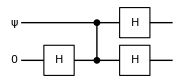

```mathematica
qc=QuantumCircuit[ProductState[S[1]->c@{0,1},"Label"->"ψ"],LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],S[{1,2},6]]
```

This is the output state.

```mathematica
out=Elaborate[qc]
```

(c_0 ␣)/(√2)+(c_0 1_S_1)/(√2)-(c_1 1_S_11_S_2)/(√2)+(c_1 1_S_2)/(√2)

As you can see here, when the first qubit is measured and the outcome is 0, then the second qubit is identical to the input state of the first qubit. In case the measurement outcome is 1, the second qubit is set to the initial state of the first qubit with the Pauli Z operated.

```mathematica
QuissoFactor[out,S[1]]//LogicalForm
```

0_S_1⊗((c_0 0_S_2)/(√2)+(c_1 1_S_2)/(√2))+1_S_1⊗((c_0 0_S_2)/(√2)-(c_1 1_S_2)/(√2))

According to the above observation, we undo the byproduct operator depending on the outcome of the measurement on the first qubit.

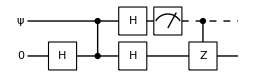

```mathematica
qc2=QuantumCircuit[qc,Measurement[S[1]],ControlledU[S[1],S[2,3]]]
```

```mathematica
new=Elaborate[qc2]/.{c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1};
QuissoFactor[new,S[1]]//LogicalForm
```

1_S_1⊗(c_0 0_S_2+c_1 1_S_2)

Consider the following quantum circuit model.

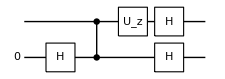

```mathematica
Let[Real,ϕ]
qc=QuantumCircuit[LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],Rotation[ϕ,S[1,3]],S[{1,2},6]]
```

This shows how the logical basis states in the first qubit is transformed through the above quantum circuit model.

```mathematica
bs=Basis[S[1]];
out=qc**bs//TrigToExp//Garner;
Thread[LogicalForm[bs]->LogicalForm[QuissoFactor[#,S[1]]&/@out,S@{1,2}]]//TableForm
```

0_S_1→0_S_1⊗((ⅇ^(-(ⅈ ϕ)/2) 0_S_2)/(√2))+1_S_1⊗((ⅇ^(-(ⅈ ϕ)/2) 0_S_2)/(√2))
1_S_1→0_S_1⊗((ⅇ^((ⅈ ϕ)/2) 1_S_2)/(√2))+1_S_1⊗(-(ⅇ^((ⅈ ϕ)/2) 1_S_2)/(√2))

When the first qubit is measured, the output state of the second qubit depends on the measurement outcome. In either case, however, the input state of the first qubit with the unitary gate operated can be recovered in the second qubit with an operation of the Pauli Z if the measurement outcome is 1.

In accordance with the above argument, the byproduct operator can be fixed as follows.

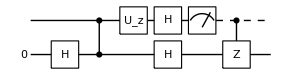

```mathematica
qc2=QuantumCircuit[qc,Measurement[S[1]],ControlledU[S[1],S[2,3]]]
```

```mathematica
new=qc2**bs//TrigToExp;
Thread[LogicalForm[bs]->LogicalForm[QuissoFactor[#,S[1]]&/@new,S@{1,2}]]//TableForm
```

0_S_1→1_S_1⊗(ⅇ^(-(ⅈ ϕ)/2) 0_S_2)
1_S_1→0_S_1⊗(ⅇ^((ⅈ ϕ)/2) 1_S_2)

### Single-Qubit Rotations

Let us construct a quantum circuit model for an arbitrary single-qubit rotation in the measurement-based scheme.

This will simplify the analysis below.

```mathematica
Let[Real,c,ϕ]
```

Here is the overall quantum circuit model. It is built in two steps divided by the vertical dashed line. The first step corresponds to the preparation, and the second to the operation.

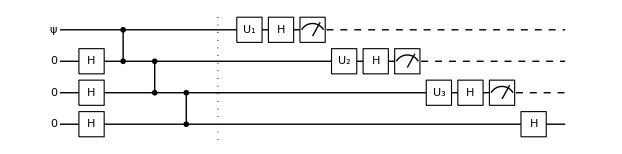

```mathematica
qc=QuantumCircuit[ProductState[S[1]->{c[0],c[1]},"Label"->Ket["ψ"]],LogicalForm[Ket[],S@{2,3,4}],S[{2,3,4},6],CZ[S[1],S[2]],CZ[S[2],S[3]],CZ[S[3],S[4]],"Separator",
Rotation[ϕ[1],S[1,3],"Label"->"U_1"],S[1,6],Measurement[S[1]],Rotation[ϕ[2],S[2,3],"Label"->"U_2"],S[2,6],Measurement[S[2]],Rotation[ϕ[3],S[3,3],"Label"->"U_3"],S[3,6],Measurement[S[3]],S[{4},6]]
```

For the sake of analysis, we build the first part of the above quantum circuit model separately.

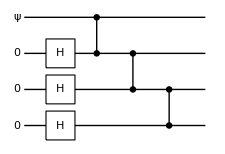

```mathematica
qc0=QuantumCircuit[
ProductState[S[1]->{c[0],c[1]},"Label"->Ket["ψ"]],
LogicalForm[Ket[],S@{2,3,4}],
S[{2,3,4},6],CZ[S[1],S[2]],CZ[S[2],S[3]],CZ[S[3],S[4]]]
```

Perform a measurement on the first qubit in a properly rotated basis.

```mathematica
out1=QuantumCircuit[qc0,Rotation[ϕ[1],S[1,3],"Label"->"U_1"],S[1,6],Measurement[S[1]]]//Elaborate;
x1=Readout[out1,S[1]]
```

1

Depending on the outcome x1 out of the measurement on the first qubit, rotate suitable the measurement setup for the second qubit and perform the measurement.

```mathematica
out2=QuantumCircuit[out1,Rotation[(-1)^x1*ϕ[2],S[2,3],"Label"->"U_2"],S[2,6],Measurement[S[2]]]//Elaborate;
x2=Readout[out2,S[2]]
```

0

Similarly, depending on the measurement outcome x2 on the second qubit, adjust the measurement setup for the third qubit and take the measurement.

```mathematica
out3=QuantumCircuit[out2,Rotation[(-1)^x2*ϕ[3],S[3,3],"Label"->"U_3"],S[3,6],Measurement[S[3]],S[4,6]]//Elaborate;
out3=out3/.{c[0]^2+c[1]^2->1};
x3=Readout[out3,S[3]]
```

0

Check the result.

```mathematica
expr=MultiplyPower[S[4,3],x3]**MultiplyPower[S[4,1],x2]**MultiplyPower[S[4,3],x1]**Rotation[ϕ[3],S[4,3]]**Rotation[ϕ[2],S[4,1]]**Rotation[ϕ[1],S[4,3]]**(Ket[S[1]->x1,S[2]->x2,S[3]->x3]**ProductState[S[4]->{c[0],c[1]}])//Elaborate
```

1_S_1 (Cos[ϕ_1/2] (c_0 Cos[ϕ_2/2]-ⅈ c_1 Sin[ϕ_2/2])+Sin[ϕ_1/2] (-ⅈ c_0 Cos[ϕ_2/2]+c_1 Sin[ϕ_2/2])) (Cos[ϕ_3/2]-ⅈ Sin[ϕ_3/2])+1_S_11_S_4 (Cos[ϕ_1/2] (-c_1 Cos[ϕ_2/2]+ⅈ c_0 Sin[ϕ_2/2])+Sin[ϕ_1/2] (-ⅈ c_1 Cos[ϕ_2/2]+c_0 Sin[ϕ_2/2])) (Cos[ϕ_3/2]+ⅈ Sin[ϕ_3/2])

```mathematica
out3-expr
```

0

### CNOT Gate

Here we demonstrate the CNOT gate based on the measurement-based scheme.

Let us consider the following quantum circuit model. The first qubit plays a role of the control qubit. The input state of the target qubit enters the second qubit and comes out on the forth qubit.

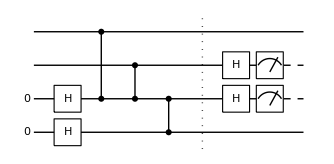

```mathematica
qc1=QuantumCircuit[LogicalForm[Ket[],S@{3,4}],S[{3,4},6],CZ[S[1],S[3]],CZ[S[2],S[3]],CZ[S[3],S[4]],"Separator",S[{2,3},6],Measurement[S@{2,3}]]
```

This shows how the logical basis states on the first two qubits are transformed to the first and forth qubit. The result is not exactly what we expect from the CNOT gate since we have not corrected the byproduct operators.

```mathematica
bs=Basis[S@{1,2}];
out=qc1**bs;
Thread[LogicalForm[bs]->LogicalForm[out,S@{1,2,3,4}]]//TableForm
```

0_S_10_S_2→0_S_11_S_20_S_30_S_4
0_S_11_S_2→0_S_10_S_21_S_30_S_4
1_S_10_S_2→1_S_10_S_20_S_31_S_4
1_S_11_S_2→1_S_10_S_21_S_31_S_4

The following quantum circuit model includes the correction of the byproduct operators.

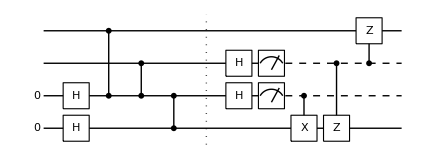

```mathematica
qc2=QuantumCircuit[qc1,ControlledU[S[3],S[4,1]],ControlledU[S[2],S[4,3]],ControlledU[S[2],S[1,3]]]
```

We see that the output state stored on the first and forth qubit is the state we expect.

```mathematica
bs=Basis[S@{1,2}];
out=qc2**bs;
Thread[LogicalForm[bs]->LogicalForm[out,S@{1,2,3,4}]]//TableForm
```

0_S_10_S_2→0_S_11_S_21_S_30_S_4
0_S_11_S_2→0_S_11_S_21_S_31_S_4
1_S_10_S_2→1_S_11_S_21_S_31_S_4
1_S_11_S_2→1_S_11_S_21_S_30_S_4

### Graph States

A graph state is created by applying the CZ gate on the two qubits linked by the graph.

For example, consider a linear graph.

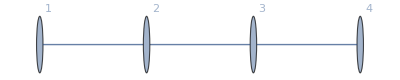

```mathematica
gr=Graph[{S[1]<->S[2],S[2]<->S[3],S[3]<->S[4]},VertexLabels->"Index"]
```

The corresponding graph state is created by the following quantum circuit model.

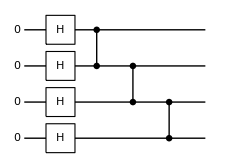

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S@{1,2,3,4}],gr]
```

```mathematica
vec=Elaborate[qc];
vec//LogicalForm
```

1/4 0_S_10_S_20_S_30_S_4+1/4 0_S_10_S_20_S_31_S_4+1/4 0_S_10_S_21_S_30_S_4-1/4 0_S_10_S_21_S_31_S_4+1/4 0_S_11_S_20_S_30_S_4+1/4 0_S_11_S_20_S_31_S_4-1/4 0_S_11_S_21_S_30_S_4+1/4 0_S_11_S_21_S_31_S_4+1/4 1_S_10_S_20_S_30_S_4+1/4 1_S_10_S_20_S_31_S_4+1/4 1_S_10_S_21_S_30_S_4-1/4 1_S_10_S_21_S_31_S_4-1/4 1_S_11_S_20_S_30_S_4-1/4 1_S_11_S_20_S_31_S_4+1/4 1_S_11_S_21_S_30_S_4-1/4 1_S_11_S_21_S_31_S_4

The same state can be directly obtained using GraphState.

```mathematica
new=GraphState[gr]
```

␣/4-1/4 1_S_11_S_2-1/4 1_S_11_S_21_S_31_S_4+(1_S_1)/4+1/4 1_S_11_S_21_S_3-1/4 1_S_11_S_21_S_4+1/4 1_S_11_S_3-1/4 1_S_11_S_31_S_4+1/4 1_S_11_S_4-1/4 1_S_21_S_3+(1_S_2)/4+1/4 1_S_21_S_31_S_4+1/4 1_S_21_S_4-1/4 1_S_31_S_4+(1_S_3)/4+(1_S_4)/4

```mathematica
vec-new//Simplify
```

0

As another example, consider the following graph and corresponding quantum circuit model.

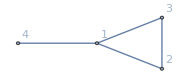

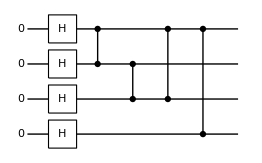

```mathematica
gr=Graph[{S[1]<->S[2],S[2]<->S[3],S[1]<->S[3],S[1]<->S[4]},ImageSize->Small,VertexLabels->"Index"]
QuantumCircuit[LogicalForm[Ket[],S@{1,2,3,4}],gr]
```

This is the graph state associated with the above graph.

```mathematica
vec=GraphState[gr]
```

␣/4-1/4 1_S_11_S_2-1/4 1_S_11_S_21_S_3+(1_S_1)/4+1/4 1_S_11_S_21_S_31_S_4+1/4 1_S_11_S_21_S_4-1/4 1_S_11_S_3+1/4 1_S_11_S_31_S_4-1/4 1_S_11_S_4-1/4 1_S_21_S_3-1/4 1_S_21_S_31_S_4+(1_S_2)/4+1/4 1_S_21_S_4+(1_S_3)/4+1/4 1_S_31_S_4+(1_S_4)/4

Here are the correlation operators associate with the vertices in the graph.

```mathematica
gnr=Stabilizer[gr]
```

{S_1^x S_2^z S_3^z S_4^z,S_1^z S_2^x S_3^z,S_1^z S_2^z S_3^x,S_1^z S_4^x}

The graph state is the simultaneous eigenstate with eigenvalue +1 of all correlation operators.

```mathematica
(gnr**vec)/vec
```

{1,1,1,1}

## Spin-Boson Model

Denote the qubits by S and the cavity mode by a.

```mathematica
Let[Qubit,S]
Let[Boson,a]
```

This is the Hamiltonian.

```mathematica
opH=Dagger[a]**a+Ω S[3]/2+g(Dagger[a]+a)**S[1]
```

a^†a+g (a S^x+a^†S^x)+(Ω S^z)/2

Here is a truncated basis.

```mathematica
bs=Basis[{a,S}];
LogicalForm@bs
```

{0_a0_S,0_a1_S,1_a0_S,1_a1_S,2_a0_S,2_a1_S,3_a0_S,3_a1_S,4_a0_S,4_a1_S,5_a0_S,5_a1_S}

Here is the matrix representation of the Hamiltonian (showing only part of it), and the eigen-energies for a particular set of parameters.  The matrix representation is not exact as the basis has been truncated.

```mathematica
Ω=1;
g=1/10;
matH=Matrix[opH];
matH[[;;6,;;6]]//MatrixForm
val=N@Eigenvalues[matH]
```

(1/2 | 0 | 0 | 1/10 | 0 | 0
0 | -1/2 | 1/10 | 0 | 0 | 0
0 | 1/10 | 3/2 | 0 | 0 | 1/(5 √2)
1/10 | 0 | 0 | 1/2 | 1/(5 √2) | 0
0 | 0 | 0 | 1/(5 √2) | 5/2 | 0
0 | 0 | 1/(5 √2) | 0 | 0 | 3/2)

{5.52494,4.7328,4.2874,3.69409,3.29609,2.66746,2.32239,1.63601,1.35389,0.594847,-0.505013,0.395102}

Here you can see the (approximate) energy levels of the spin-boson model.

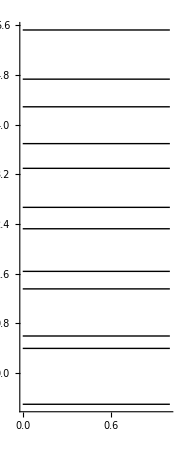

```mathematica
levels=Line@Thread@{Thread@{0,val},Thread@{1,val}};
Graphics[levels,
BaseStyle->Thick,
Axes->{None,True}]
```